Example 1, p 100

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=y''[x]+y[x]==Sec[x]
```

y[x]+y''[x]==Sec[x]

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

```mathematica
frx=Collect[sol,{Cos[x],Sin[x]}]
```

{{y→Function[{x},C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]]}}

Above: The answer is correct, except for the Cos[x] which is the argument of Log. This argument should be an absolute value. Putting in the Abs[] makes for a nice-looking solution, but I have no clue how to diagnose its desirability.

```mathematica
grx=frx/.{C[1]->1,C[2]->1}
```

{{y→Function[{x},1 Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+1 Sin[x]]}}

```mathematica
xrx=Cos[x] (1+Log[Abs[Cos[x]]])+(x+1) Sin[x]
```

Cos[x] (1+Log[Abs[Cos[x]]])+(1+x) Sin[x]

Here I get a couple of initial values for use for NDSolve. The accuracy of location of the first can be seen on the colored plot below.

```mathematica
(Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+1 Sin[x])/.x->0
```

1

```mathematica
D[(Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+1 Sin[x]),x]
```

Cos[x]+x Cos[x]-Sin[x]-Log[Cos[x]] Sin[x]

```mathematica
(Cos[x]+x Cos[x]-Sin[x]-Log[Cos[x]] Sin[x])/.x->0
```

1

```mathematica
s2=NDSolve[{eqn,y[0]==1,y'[0]==1},y,{x,-6-6},Method->"ImplicitRungeKutta"]
```

NDSolve::ndsz: At x == -1.5708, step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[{{-1.5708, 0.}}, <>]}}

Using NDSolve does me no good at all. I was hoping it would fix the problem with the gaps in the plot, but it looks meaningless.

```mathematica
Plot[Evaluate[y[x]/.s2],{x,-6,6},PlotRange->All,ImageSize->250]
```

InterpolatingFunction::dmval: Input value {-5.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
plot1=Plot[y[x]/.grx,{x,-8,8},PlotRange->Automatic,PlotStyle->{Yellow,Thickness[0.004]}];
plot2=Plot[xrx,{x,-8,8},PlotRange->Automatic,PlotStyle->{Red,Thickness[0.015]}];
```

Looking at the plot of the RHS of the original problem might have given a clue to trouble ahead.

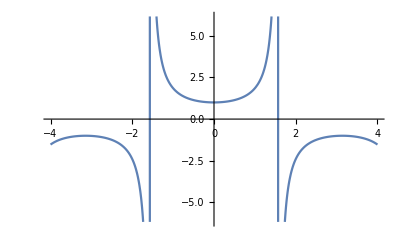

```mathematica
Plot[Sec[x],{x,-4,4}]
```

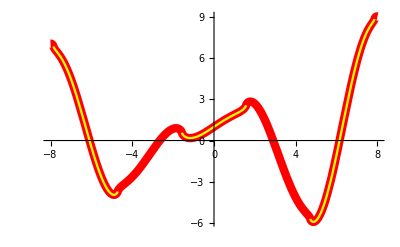

```mathematica
Show[plot2,plot1]
```

The Mathematica function is in yellow, and the text version, with Abs, is in red. The question is, how is it to be detected that the solution by Mathematica is flawed and how is it to be understood what correction needs to be made?

1 - 13 General solution
Solve the given nonhomogeneous linear ODE by variation of parameters or undetermined coefficients.

1.  y'' + 9 y = Sec[3 x]

```mathematica
Clear["Global`*"]
```

```mathematica
has=y''[x]+9 y[x]==Sec[3 x]
bas=DSolve[has,y[x],x]
```

9 y[x]+y''[x]==Sec[3 x]

{{y[x]→C[1] Cos[3 x]+C[2] Sin[3 x]+1/9 (Cos[3 x] Log[Cos[3 x]]+3 x Sin[3 x])}}

1. Above: This is one case where Mathematica comes up with the text answer without significant simplification.

```mathematica
nas=bas/.{C[1]->A,C[2]->B}
```

{{y[x]→A Cos[3 x]+B Sin[3 x]+1/9 (Cos[3 x] Log[Cos[3 x]]+3 x Sin[3 x])}}

2. Above: The slightly altered form matches the text answer.

3.  x^2 y''-2x y'+2y=x^3 Sin[x]

```mathematica
Clear["Global`*"]
```

```mathematica
din=x^2 y''[x]-2 x y'[x]+2 y[x]==x^3 Sin[x]
fin=DSolve[din,y[x],x]
```

2 y[x]-2 x y'[x]+x^2 y''[x]==x^3 Sin[x]

{{y[x]→x C[1]+x^2 C[2]-x Sin[x]}}

1. Above: Mathematica produces the text answer on the first try.

5.  y'' + y = Cos[x] - Sin[x]

```mathematica
Clear["Global`*"]
```

```mathematica
sar=y''[x]+y[x]==Cos[x]-Sin[x]
zar=DSolve[sar,y[x],x]
```

y[x]+y''[x]==Cos[x]-Sin[x]

{{y[x]→C[1] Cos[x]+C[2] Sin[x]+1/4 (2 x Cos[x]+2 Cos[x]^3+2 x Sin[x]+2 Cos[x]^2 Sin[x]-Cos[x] Sin[2 x]+Sin[x] Sin[2 x])}}

```mathematica
mar=Expand[zar]
```

{{y[x]→1/2 x Cos[x]+C[1] Cos[x]+Cos[x]^3/2+1/2 x Sin[x]+C[2] Sin[x]+1/2 Cos[x]^2 Sin[x]-1/4 Cos[x] Sin[2 x]+1/4 Sin[x] Sin[2 x]}}

```mathematica
yar=TrigReduce[mar]
```

{{y[x]→1/2 (Cos[x]+x Cos[x]+2 C[1] Cos[x]+x Sin[x]+2 C[2] Sin[x])}}

```mathematica
Collect[yar,x]
```

{{y[x]→1/2 x (Cos[x]+Sin[x])+1/2 (Cos[x]+2 C[1] Cos[x]+2 C[2] Sin[x])}}

1. Above: The expression ‘yar’ looks pretty good. However, getting Mathematica to refine it further is a challenge.

```mathematica
yar1=1/2 x (Cos[x]+Sin[x])
```

1/2 x (Cos[x]+Sin[x])

2. Above: I resorted to splitting the expression into two pieces. ‘yar1’ is the first piece.

```mathematica
yar2=1/2 (Cos[x]+2 C[1] Cos[x]+2 C[2] Sin[x])
```

1/2 (Cos[x]+2 C[1] Cos[x]+2 C[2] Sin[x])

3. Above: ‘yar2’ is the second piece.

```mathematica
ear2=Simplify[yar2]
```

(1/2+C[1]) Cos[x]+C[2] Sin[x]

```mathematica
war2=ear2/.{(1/2+C[1])->A,C[2]->B}
```

A Cos[x]+B Sin[x]

4. Above: I was finally able to replace constant names.

```mathematica
out=yar1+war2
```

A Cos[x]+B Sin[x]+1/2 x (Cos[x]+Sin[x])

5. The above form matches the text answer.

7.  (D^2-4 D+4 I)y=6 ⅇ^(2x/x^4)

```mathematica
Clear["Global`*"]
```

```mathematica
sop=y''[x]-4 y'[x]+4 y[x]==(6 ⅇ^(2 x))/x^4
drop=DSolve[sop,y[x],x]
```

4 y[x]-4 y'[x]+y''[x]==(6 ⅇ^(2 x))/x^4

{{y[x]→ⅇ^(2 x)/x^2+ⅇ^(2 x) C[1]+ⅇ^(2 x) x C[2]}}

1. Above: Appropriate assignment of arbitrary coefficients makes the answer agree with the text’s.

9.  (D^2-2D+I)y=35 x^(3/2)ⅇ^x

```mathematica
Clear["Global`*"]
```

```mathematica
gat=y''[x]-2 y'[x]+y[x]==35 x^(3/2) ⅇ^x
fat=DSolve[gat,y[x],x]
```

y[x]-2 y'[x]+y''[x]==35 ⅇ^x x^(3/2)

{{y[x]→4 ⅇ^x x^(7/2)+ⅇ^x C[1]+ⅇ^x x C[2]}}

1. Above: Appropriate assignment of arbitrary coefficients makes the answer agree with the text’s.

11.  (x^2 D^2-4x D+6I)y=21 x^-4

```mathematica
Clear["Global`*"]
```

```mathematica
stek=x^2 y''[x]-4 x y'[x]+6 y[x]==21 x^-4
peck=DSolve[stek,y[x],x]
```

6 y[x]-4 x y'[x]+x^2 y''[x]==21/x^4

{{y[x]→1/(2 x^4)+x^2 C[1]+x^3 C[2]}}

1. Above: The answer matches the text’s.

13.  (x^2 D^2+x D-9I)y=48 x^5

```mathematica
Clear["Global`*"]
```

```mathematica
naru=x^2 y''[x]+x y'[x]-9 y[x]==48 x^5
garu=DSolve[naru,y[x],x]
```

-9 y[x]+x y'[x]+x^2 y''[x]==48 x^5

{{y[x]→4 x^2 Cosh[3 Log[x]]-x^8 Cosh[3 Log[x]]+C[1] Cosh[3 Log[x]]+4 x^2 Sinh[3 Log[x]]+x^8 Sinh[3 Log[x]]+ⅈ C[2] Sinh[3 Log[x]]}}

```mathematica
haru=FullSimplify[TrigReduce[garu]]
```

{{y[x]→(6 x^8+C[1]+x^6 C[1]+ⅈ (-1+x^6) C[2])/(2 x^3)}}

```mathematica
baru=haru/.(-1+x^6)->0
```

{{y[x]→(6 x^8+C[1]+x^6 C[1])/(2 x^3)}}

```mathematica
paru=Apart[baru]
```

{{y[x]→3 x^5+((1+x^6) C[1])/(2 x^3)}}

```mathematica
maru=ExpandNumerator[paru]
```

{{y[x]→3 x^5+(C[1]+x^6 C[1])/(2 x^3)}}

```mathematica
yaru=maru/.((C[1]+x^6 C[1])/(2 x^3))->(C[1]/(2 x^3)+(x^6 C[1])/(2 x^3))
```

{{y[x]→3 x^5+C[1]/(2 x^3)+1/2 x^3 C[1]}}

```mathematica
saru=yaru/.{C[1]/(2 x^3)->C[3]/x^3,1/2 x^3 C[1]->C[3] x^3}
```

{{y[x]→3 x^5+C[3]/x^3+x^3 C[3]}}

1. Above: The expression matches the text answer.